# Simulating Data

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
SetDirectory["C:/Users/User/Goliath/resources"];
```

## SHO oscillator

```mathematica
L[th1_, w1_]:= w1^2 - th1^2;
```

Generate the Euler Equations

```mathematica
sol=EulerEquations[L[th1[t],  D[th1[t],t]], th1[t], t]
```

-2 (th1[t]+th1''[t])==0

```mathematica
sol1=NDSolve[{sol, th1[0]==1, th1[1]==1}, th1[t], {t,0,100.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

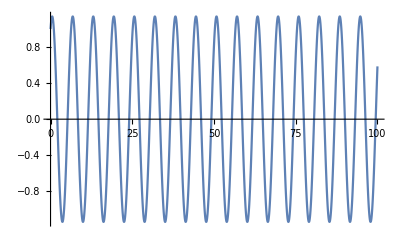

```mathematica
Plot[Evaluate[th1[t]/.sol1], {t, 0,100.0}, PlotRange->All]
```

```mathematica
deltat = 0.01
```

0.01

```mathematica
times = Range[0,100, deltat];
```

```mathematica
expth1 = Flatten[(th1[t]/.sol1)/.t->times];
```

```mathematica
results=Transpose[{expth1}];
```

```mathematica
Export["sho_0.01.csv", results, "CSV"];
```

## Coupled SHO

```mathematica
L1[th1_, th2_,  w1_, w2_]:= w1^2 + w2^2 - 2 th1^2 -  th2^2 + 2 th1 th2;
```

Generate the Euler Equations

```mathematica
sol2=EulerEquations[L1[th1[t], th2[t],  D[th1[t],t], D[th2[t],t] ], {th1[t], th2[t]}, t]
```

{-2 (2 th1[t]-th2[t]+th1''[t])==0,2 (th1[t]-th2[t]-th2''[t])==0}

```mathematica
sol3=NDSolve[{sol2, th1[0]==1, th1[1]==1, th2[0]== 2, th2[1]== 1}, {th1[t], th2[t]}, {t,0,100.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 100.}}, <>][t],th2[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

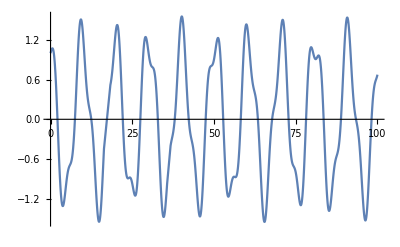

```mathematica
Plot[Evaluate[th1[t]/.sol3], {t, 0,100.0}, PlotRange->All]
```

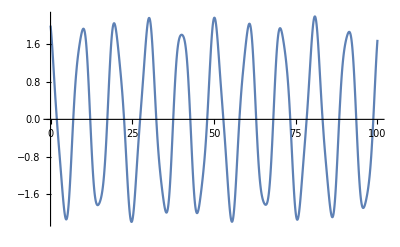

```mathematica
Plot[Evaluate[th2[t]/.sol3], {t,0,100.0}, PlotRange->All]
```

```mathematica
deltat1 = 0.01
```

0.01

```mathematica
times1= Range[0,100, deltat1];
```

```mathematica
expth11 = Flatten[(th1[t]/.sol3)/.t->times1];
```

```mathematica
expth12 = Flatten[(th2[t]/.sol3)/.t->times1];
```

```mathematica
results1=Transpose[{expth11, expth12}];
```

```mathematica
Export["sho_coupled_0.01.csv", results1, "CSV"];
```